```mathematica
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/sextupoleResults.json"];
raw= Association[#]&/@raw;
```

```mathematica
groupedData = GroupBy[raw,{#sextName,#bpmName, #magnetConfig, #axis}&];
```

```mathematica
sextNames = raw[[All,"sextName"]]//DeleteDuplicates;
bpmNames=  raw[[All,"bpmName"]]//DeleteDuplicates;
```

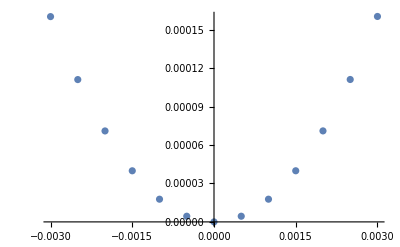

```mathematica
ListPlot[
{#sextOffset,#bpmXOffset}&/@groupedData[[10]]
]
```

```mathematica
allImg= Table[
img = GraphicsGrid[
Table[
activeData = {
10^3#sextOffset,
10^3#[[bpmAxis]]
}&/@groupedData[{sextName,bpmName,magnetConfig,moverAxis}];

ListPlot[
activeData,
PlotLabel->{sextName,bpmName,magnetConfig,moverAxis},
ImageSize->400,
Frame->True,
FrameLabel->{sextName<>" offset [mm]", bpmName<>" offset [mm]"},
(*PlotStyle->ColorData["Rainbow"][Rescale[Max[Abs[activeData[[All,2]]]],{0,0.5}]]*)
ColorFunctionScaling->False,
ColorFunction->(ColorData["Rainbow"][Rescale[Max[Abs[#2]],{0,0.2}]]&),
Joined->True
],

{sextName,sextNames},
{bpmName,bpmNames}

],
ImageSize->4000
];

Export["~/"<>StringRiffle[{magnetConfig,moverAxis,bpmAxis},"_"]<>".png",img];
img,

{magnetConfig,{"BCON","BMAX"}},
{moverAxis,{"x","y"}},
{bpmAxis,{"bpmXOffset","bpmYOffset"}}
];
```

```mathematica
allImg= Table[
img = GraphicsGrid[
Table[
activeXData = {
10^3#sextOffset,
10^3#bpmXOffset
}&/@groupedData[{sextName,bpmName,magnetConfig,moverAxis}];
activeYData = {
10^3#sextOffset,
10^3#bpmYOffset
}&/@groupedData[{sextName,bpmName,magnetConfig,moverAxis}];

Show[
ListPlot[
{activeXData,activeYData},
PlotLabel->{sextName,bpmName,magnetConfig,moverAxis},
ImageSize->400,
Frame->True,
FrameLabel->{sextName<>" offset [mm]", bpmName<>" offset [mm]"},
(*PlotStyle->ColorData["Rainbow"][Rescale[Max[Abs[activeData[[All,2]]]],{0,0.5}]]*)
ColorFunctionScaling->False,
ColorFunction->(ColorData["Rainbow"][Rescale[Max[Abs[#2]],{0,0.2}]]&),
Joined->True
],
ListPlot[
{activeXData,activeYData},
PlotStyle->Black,
PlotMarkers->{"X","Y"}
]],

{sextName,sextNames},
{bpmName,bpmNames}

],
ImageSize->4000
];

Export["~/"<>StringRiffle[{magnetConfig,moverAxis},"_"]<>".png",img];
img,

{magnetConfig,{"BCON","BMAX"}},
{moverAxis,{"x","y"}}
];
```

## Y data with offsets

```mathematica
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/sextupoleResults_withOffsets.json"];
raw= Association[#]&/@raw;
```

```mathematica
groupedData = GroupBy[raw,{#sextName,#bpmName, #magnetConfig, #axis}&];
```

```mathematica
allImg= Table[
img = GraphicsGrid[
Table[
activeXData = {
10^3#sextOffset,
10^3#bpmXOffset
}&/@groupedData[{sextName,bpmName,magnetConfig,moverAxis}];
activeYData = {
10^3#sextOffset,
10^3#bpmYOffset
}&/@groupedData[{sextName,bpmName,magnetConfig,moverAxis}];

Show[
ListPlot[
{activeXData,activeYData},
PlotLabel->{sextName,bpmName,magnetConfig,moverAxis},
ImageSize->400,
Frame->True,
FrameLabel->{sextName<>" offset [mm]", bpmName<>" offset [mm]"},
(*PlotStyle->ColorData["Rainbow"][Rescale[Max[Abs[activeData[[All,2]]]],{0,0.5}]]*)
ColorFunctionScaling->False,
ColorFunction->(ColorData["Rainbow"][Rescale[Max[Abs[#2]],{0,0.2}]]&),
Joined->True
],
ListPlot[
{activeXData,activeYData},
PlotStyle->Black,
PlotMarkers->{"X","Y"}
]],

{sextName,sextNames},
{bpmName,bpmNames}

],
ImageSize->4000
];

Export["~/"<>StringRiffle[{magnetConfig,moverAxis},""]<>"_withOffsets.png",img];
img,

{magnetConfig,{"BCON","BMAX"}},
{moverAxis,{"y"}}
];
```